# Machine Learning

## Part 3: Support Vector Classification

In this article we go deeper into the theory of support vector classification, treating regularization, duality, and kernels.

Yen Lee Loh, 2022-12-9

## Section The binary classification problem

Suppose we are given a set of training input vectors x_n and training outputs y_n∈{-1,+1} for n=1,2,3,…,N.  The input vectors form a set of N points in D-dimensional space.  In the figure below, N=25 and D=2.  Green disks have y_n=+1 and red disks have y_n=-1.  We wish to find a boundary that separates the two classes of points as well as possible.  This is known as binary classification.

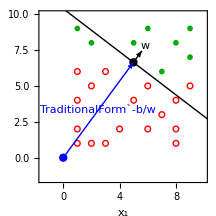

For any vector w, note that w·x+b=0 is the equation of a boundary hyperplane (black line) normal to w and passing through the point x=-b/w^2w (black dot).  The perpendicular distance from the origin to the the boundary is d=-b/w (blue arrow).

It is useful to define the linear predictor u=w·x+b.  The decision boundary is the hyperplane u=0, which divides space into two regions, u>0 and u<0.  Ideally, the region u>0 contains only points with y>0, and the region u<0 contains only points with y<0.  That is, the boundary separates the green disks and the red circles neatly into two categories.  Let F_count be the total number of misclassified examples.  This is a step function of u, as illustrated in the first panel below:
	F_count=∑_(n=1)^N f_count(y_n u_n),	f_count(yu)=Θ(-yu)=Piecewise[{{0, if y and u have the same sign}, {1, if y and u have opposite signs.}}]

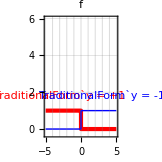
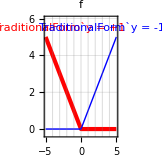
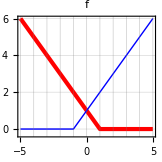
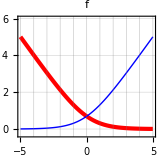

We wish to choose w and b to minimize F_count.  Ideally, F_count=0.  In panel (c), there are two green disks and one red circle that have been misclassified, so F_count=3 (and the error rate is 3/25=12%).  The problems with this approach are:
1.  F_count is an integer.  F_count(w) is discontinuous, with steps and plateaus.  The gradient (∂F_count)/(∂w) is zero everywhere.  
      If F_count>0, we are unable to use gradient descent to tell us how we should change w to improve the classification.
2.  If F_count=0, even though the boundary satisfies our criteria, it may not be the best answer because it may graze one or more points, 
      and may not pass squarely through the middle of the “no-man’s land”.
3.  f_count does not take into account whether a misclassified example is a “borderline case” or a “severely misclassified case”.
4.  f_count remains invariant if both w and b are scaled by the same constant.  Therefore the solution is not uniquely determined.

We may address problem 1 and 3 above by defining a distance-based cost function (see second panel above).  Let each misclassified point contribute a cost proportional to its perpendicular distance from the decision boundary.  (Drop these perpendiculars.)  Then the total cost is the total length of the perpendiculars.
	F_dist=∑_(n=1)^N f_dist(y_n u_n)	where f_dist(yu)=ramp(-yu)=-yu Θ(-yu)=Piecewise[{{0, if y and u have the same sign}, {-yu, if y and u have opposite signs.}}]

We may address problem 4 by imposing the constraint that w is a unit vector.  However, the standard SVC algorithm, which we describe below, address all four problems.

## Section Basic support vector classification

A support vector machine (SVM) is a model for support vector classification (SVC).  SVC is an algorithm for performing binary classification by minimizing the hinge loss function applied.08to the linear predictor. 
	F_SVC=∑_(n=1)^N f_SVC(y_n u_n),	f_SVC(yu)=ramp(1-yu)=Piecewise[{{0, if the point is in the correct zone,within the near margin}, {1-yu, if the point is beyond the near margin of the correct zone}}]
where u=w·x+b.  This cost function is visualized below.  Green and red circles represent input vectors x_n=(x_1,x_2) corresponding to outputs y_n=+1 and y_n=-1 respectively.  The solid orange line is the decision boundary w·x+b=0.  The dashed orange lines are the margins.  If a point lies beyond the near margin of its “zone,” it contributes a penalty, given by the hinge loss function, which is proportional to the perpendicular distance from that margin.  This distance is indicated by a stem.  (TBD: shade regions)

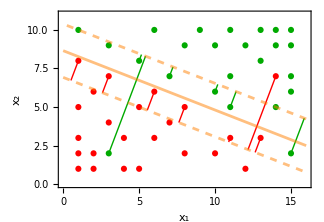

“Training a support vector machine” means adjusting w and b to minimize F_SVC.  We may evaluate the gradient of F_SVC analytically:
	(∂F_SVC)/(∂w_i)=∑_(n=1)^N (∂f_SVC)/(∂u_n)(∂u_n)/(∂w_i)=∑_(n=1)^N (-y_n)Θ(1-y_n u_n)x_i
	(∂F_SVC)/(∂b)=∑_(n=1)^N (∂f_SVC)/(∂u_n)(∂u_n)/(∂b)=∑_(n=1)^N (-y_n)Θ(1-y_n u_n).
This allows us to use gradient descent to minimize F_SVC.

## Section Regularization

For linear SVC I don’t think overfitting is usually a problem.  However, later on (or in the examples) we will see that SVC with a kernel can suffer from overfitting.  Therefore, one sometimes includes a regularizer in the SVC function, to reduce overfitting.  The documentation for LIBLINEAR (Rong-En Fan et al., 2017) gives a good overview of various common types of SVC and logistic regression.  (From here onwards, w·x is understood to mean w·x+b.)

L2-regularized L1-loss SVC:			Minimize F(w)=∑_(n=1)^N max(0,1-y_n w·x_n)+λ w^T w	(default)
L2-regularized L2-loss SVC:			Minimize F(w)=∑_(n=1)^N [max(0,1-y_n w·x_n)]^2+λ w^T w
L2-regularized logistic regression:		Minimize F(w)=-∑_(n=1)^N ln (1+e^(-yw·x_n))+λ w^T w

L1-regularized versions are also available, in which one uses λ(||w||)_1 instead of λ w^T w for the regularizer.

The first term is a penalty term.  The second term is a regularizer.  The parameter λ tunes the behavior of SVC.  λ=0 corresponds to a hard-margin classifier with no regularization.  λ=100 corresponds to a soft-margin classifier.

## Section Dual forms

In classification, the primal problem refers to minimizing the objective function F(w) with respect to the weight vector w.  Note that w=(w_1,…,w_D) is a vector in the feature space, i.e., the space of input vectors.

It turns out that using the properties of Legendre transformations, the primal problem may be transformed into a dual problem where one minimizes a dual objective function F̃(W) with respect to the vector W.  Note that W=(W_1,…,W_N), where N is the number of data points!

For each primal problem above, the LIBLINEAR documentation gives the corresponding dual problem:

L2-reg L1-loss SVC:	Min F̃(W)=∑_(n=1)^N ∑_(n'=1)^N 1/2 y_n y_n' x_n^T x_n' W_n W_n'-λ∑_(n=1)^N W_n subject to 0≤W_n≤1
L2-reg L2-loss SVC:	Min F̃(W)=∑_(n=1)^N ∑_(n'=1)^N 1/2 y_n y_n' x_n^T x_n' W_n W_n'+λ∑_(n=1)^N 1/4 W_n(W_n-4/λ) subject to  0≤W_n≤∞ 
L2-reg LR:		Min F̃(W)=∑_(n=1)^N ∑_(n'=1)^N 1/2 y_n y_n' x_n^T x_n' W_n W_n'+λ∑_(n=1)^N [W_n ln W_n+(1-W_n)ln(1-W_n)]	 subject to 0≤W_n≤1.
The constraints may be written using infinite step functions if one prefers.   (Warning: I have not checked my translation from the LIBLINEAR docs carefully!)

After minimizing F̃(W) w.r.t. W, one may recover the primal weights from the dual weights using w=1/λ∑_(n=1)^N y_n x_n W_n.  This shows that the dual weight W_n describes “how much” the data point (x_n,y_n) influences the decision boundary.

We see that:
(a)  In the dual representation, SVC corresponds to quadratic programming (minimizing a quadratic form subject to constraints).  
      Efficient algorithms exist for this.   [TBD: illustration with contours and boundaries]
(b)  The regularizer terms (the second terms that don’t involve the data values x and y) come with a factor of λ. 
(c)  The regularizer terms are of the form (f̃)_reg(α_n) where (f̃)_reg is a non-strictly-convex function.  Thus the algorithm tends to lean towards giving all points equal weight, unless there is a reason not to.  See figure below (scaling is arbitrary.)

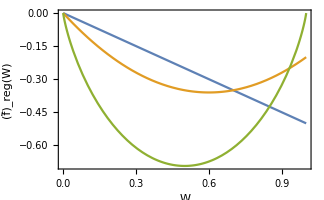

```mathematica
Plot[{-.5W,W(W-1.2),W Log[W]+(1-W)Log[1-W]},{W,0,1},FrameLabel->{"W","(f̃)_reg(W)"}]
```

Is it better to use the primal or dual problem representation?  
The primal objective function F(w)=∑_(n=1)^N max(0,1-y_n w·x_n)+λ w^T w takes O(ND) operations to evaluate.

For the dual problem, one precalculates the matrix Q_(n n')=y_n y_n' x_n^T x_n', which takes O(N^2 D) operations and O(N^2) storage.
Then, the dual objective function F̃(W)=∑_(n=1)^N ∑_(n'=1)^N 1/2 Q_(n n')W_n W_n'-λ∑_(n=1)^N W_n takes O(N^2) operations to evaluate.

Suppose you are training a SVC on the MNIST Database of Handwritten Digits data set, which consists of N=60000 training examples.  Each example is a 28×28 matrix of integers between 0 and 255.  Thus the number of features (pixels) is D=784.  In this case D≪N.  The primal representation is likely to be faster.  Moreover, in the dual representation, storing {Q_(n n')} in double precision requres 29 GB of memory, which is prohibitive.

On the other hand, if one has a small number of examples with N≪D, then the dual representation may be good. (What do the books say about this?)

In my opinion, the main reason for studying the dual representation is to understand the kernel trick, which we encounter later.

## Section Demonstrations

### Section.Subsection Demonstration: Linearly separable data

Run the code below to define the functions svmTrainPrimal[] and svmTrainDual[], which solve the following problems:
Primal problem: minimize F(w)=∑_(n=1)^N max(0,1-y_n w·x_n)+λ w^T w.
Dual problem: precalculate K_(n n')=x_n^T x_n' and Q_(n n')=y_n y_n' K_(n n'), then minimize F̃(W)=∑_(n=1)^N ∑_(n'=1)^N 1/2 Q_(n n')W_n W_n'-λ∑_(n=1)^N W_n subject to 0≤W_n≤1. 
Note that w=1/λ∑_(n=1)^N y_n x_n W_n.

```mathematica
(*-------- TRAIN SVM BINARY CLASSIFIER BY BRUTE-FORCE MINIMIZATION OF PRIMAL OBJECTIVE FUNCTION --------*)
svmTrainPrimal[xnd_,yn_,λ_]:=Module[{f,w,nmax,dmax,wdVars},
{nmax,dmax}=Dimensions@xnd;
f[wd_]:=Sum[  Max[0.,1.-yn⟦n⟧*wd.xnd⟦n⟧] ,{n,nmax}]+λ/2 wd.wd;
wdVars=Table[Subscript[w, d],{d,dmax}];
Last/@Last@NMinimize[f[wdVars],wdVars]
];
(*-------- TRAIN SVM BINARY CLASSIFIER BY BRUTE-FORCE MINIMIZATION OF DUAL OBJECTIVE FUNCTION --------*)
svmTrainDual[xnd_,yn_,λ_]:=Module[{FDual,W,Knn,Qnn,nmax,dmax,wdVars},
{nmax,dmax}=Dimensions@xnd;
Knn=xnd.xndᵀ;  (* kernel matrix *)
Qnn=KroneckerProduct[yn,yn]*Knn;
FDual[Wn_]:=1/2 Wn.Qnn.Wn-λ*Total[Wn];
WnVars=Table[Subscript[W, n],{n,nmax}];
constraints=Table[0≤Subscript[W, n]≤1,{n,nmax}];
Last/@Last@NMinimize[{FDual[WnVars],constraints},WnVars,AccuracyGoal->6]//Chop[#,10^-6]&
];
```

The code below is long and messy – just run it to define the visualize function.

```mathematica
visualize[]:=Module[{},
radius=.2;
grPrimal=Show[
(*-------- Plot training data points --------*)
Graphics[{
Table[{
xd=Rest@xndTrain⟦n⟧;
If[ynTrain⟦n⟧>0,Darker@Green,Red],     (* pick color *)
Disk[xd,radius],     (* draw datapoint *)
If[1-ynTrain⟦n⟧*wd.xndTrain⟦n⟧>0,Line[{xd,xd-(wd.xndTrain⟦n⟧-ynTrain⟦n⟧)/(wd⟦-2⟧^2+wd⟦-1⟧^2){wd⟦-2⟧,wd⟦-1⟧}}]]     (* draw line indicating penalty for misclassified point *)
},{n,nmax}]
},PlotRange->{{0,imax+1},{0,jmax+1}}],
(*-------- Plot decision boundary and margin --------*)
ContourPlot[wd.{1,x1,x2},{x1,0,imax+1},{x2,0,jmax+1},Contours->{-1,0,1},ContourStyle->{{Dashed,Orange,AbsoluteThickness@2},{Orange,AbsoluteThickness@2},{Dashed,Orange,AbsoluteThickness@2}},ContourShading->False],
Frame->True,FrameLabel->{"x_1","x_2"},FrameStyle->Black,RotateLabel->False,ImageSize->324,BaseStyle->{16,Black,FontFamily->"Times"}
];
grDual=Show[
Graphics[{
AbsoluteThickness@0,
Table[{
xd=Rest@xndTrain⟦n⟧;
If[ynTrain⟦n⟧>0,Darker@Green,Red],     (* pick color *)
Circle[xd,radius],     (* draw datapoint as empty circle *)
Disk[xd,radius,{0,2π*Wn⟦n⟧}]     (* fill datapoint as wedge according to weight (0≤W≤1) *)
},{n,nmax}]
},PlotRange->{{0,imax+1},{0,jmax+1}}],
Frame->True,FrameLabel->{"x_1","x_2"},FrameStyle->Black,RotateLabel->False,ImageSize->324,BaseStyle->{16,Black,FontFamily->"Times"}
];
Row@{grPrimal,grDual}
];
```

Run the code below.  You can try changing the data map to see what happens.

{-16.,0.75,1.75}

{-15.9998,0.751295,1.75034}

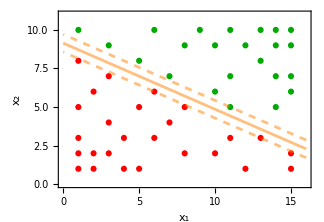
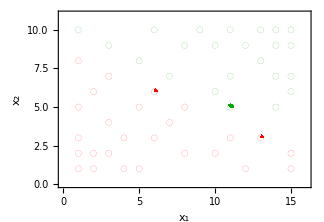

```mathematica
(*-------- SET UP TRAINING INPUTS xndTrain AND TRAINING OUTPUTS ynTrain --------*)
map=({{1, □, □, □, □, 1, □, □, 1, □, 1, □, 1, 1, 1}, {□, □, 1, □, □, □, □, 1, □, 1, □, 1, □, 1, 1}, {0, □, □, □, 1, □, □, □, □, □, □, □, 1, □, □}, {□, □, 0, □, □, □, 1, □, □, □, 1, □, □, 1, 1}, {□, 0, □, □, □, 0, □, □, □, 1, □, □, □, □, 1}, {0, □, □, □, 0, □, □, 0, □, □, 1, □, □, 1, □}, {□, □, 0, □, □, □, 0, □, □, □, □, □, □, □, □}, {0, □, □, 0, □, 0, □, □, □, □, 0, □, 0, □, □}, {0, 0, 0, □, □, □, □, 0, □, 0, □, □, □, □, 0}, {0, 0, □, 0, 0, □, □, □, □, □, □, 0, □, □, 0}})//Reverse//Transpose;
{imax,jmax}=Dimensions@map;
xndTrain=Position[map,0]~Join~Position[map,1]; (* you may want to examine contents of these *)
ynTrain=map⟦#⟦1⟧,#⟦2⟧⟧&/@xndTrain/.{0->-1}; (* our definition of SVM uses +1 and -1 as class labels *)
xndTrain=Prepend[#,1]&/@xndTrain; (* prepend Subscript[x, 0]=1 to each input vector *)
{nmax,dmax}=Dimensions@xndTrain;
(*-------- DO THE TRAINING BOTH WAYS TO OBTAIN PRIMAL WEIGHTS Subscript[w, d] AND DUAL WEIGHTS Subscript[W, n] --------*)
λ=.003;
wd=svmTrainPrimal[xndTrain,ynTrain,λ];
Wn=svmTrainDual[xndTrain,ynTrain,λ];
(*-------- VERIFY THAT PRIMAL WEIGHTS CAN BE RECOVERED FROM DUAL WEIGHTS  --------*)
wd
Total[(Wn*ynTrain)*xndTrain]/λ
(*-------- MAKE THE PLOTS  --------*)
visualize[]
```

(Left)  Green and red circles represent input vectors x_n=(1,x_1,x_2) corresponding to outputs y_n=+1 and y_n=-1 respectively.  (We use the usual trick of setting x_0=1 to allow bias.)  In this case, the data are linearly separable, and we have used a hard-margin classifier (SVC with a very small regularization parameter λ=0.003).  Then, SVC gives the decision boundary w·x=0 as the maximum-margin hyperplane (solid orange line).  The dashed orange lines indicate the margin; we will refer to them as margins.

(Right)  SVC was performed on the same dataset, but in the dual representation.  This gives dual weights W_n∈[0,1] representing the relative importance of each data point when performing classification.  For each point W_n is represented by a pie slice.  In the present situation, the only points that have any weight are the points that touch the margins.  These points are called support vectors.

### Section.Subsection Demonstration: Data that are not linearly separable

Run the code below AFTER running the previous section!

{-5.,0.222222,0.577778}

{-5.,0.222225,0.577786}

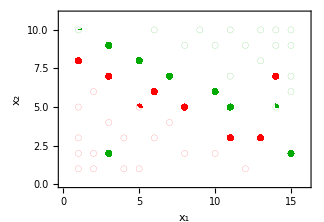
-Graphics--Graphics-

```mathematica
(*-------- SET UP TRAINING INPUTS xndTrain AND TRAINING OUTPUTS ynTrain --------*)
map=({{1, □, □, □, □, 1, □, □, 1, □, 1, □, 1, 1, 1}, {□, □, 1, □, □, □, □, 1, □, 1, □, 1, □, 1, 1}, {0, □, □, □, 1, □, □, □, □, □, □, □, 1, □, □}, {□, □, 0, □, □, □, 1, □, □, □, 1, □, □, 0, 1}, {□, 0, □, □, □, 0, □, □, □, 1, □, □, □, □, 1}, {0, □, □, □, 0, □, □, 0, □, □, 1, □, □, 1, □}, {□, □, 0, □, □, □, 0, □, □, □, □, □, □, □, □}, {0, □, □, 0, □, 0, □, □, □, □, 0, □, 0, □, □}, {0, 0, 1, □, □, □, □, 0, □, 0, □, □, □, □, 1}, {0, 0, □, 0, 0, □, □, □, □, □, □, 0, □, □, □}})//Reverse//Transpose;
{imax,jmax}=Dimensions@map;
xndTrain=Position[map,0]~Join~Position[map,1]; (* you may want to examine contents of these *)
ynTrain=map⟦#⟦1⟧,#⟦2⟧⟧&/@xndTrain/.{0->-1}; (* our definition of SVM uses +1 and -1 as class labels *)
xndTrain=Prepend[#,1]&/@xndTrain; (* prepend Subscript[x, 0]=1 to each input vector *)
{nmax,dmax}=Dimensions@xndTrain;
(*-------- DO THE TRAINING BOTH WAYS TO OBTAIN PRIMAL WEIGHTS Subscript[w, d] AND DUAL WEIGHTS Subscript[W, n] --------*)
λ=.01;
wd=svmTrainPrimal[xndTrain,ynTrain,λ];
Wn=svmTrainDual[xndTrain,ynTrain,λ];
(*-------- VERIFY THAT PRIMAL WEIGHTS CAN BE RECOVERED FROM DUAL WEIGHTS  --------*)
wd
Total[(Wn*ynTrain)*xndTrain]/λ
(*-------- MAKE THE PLOTS  --------*)
visualize[]
```

(Left)  Green and red circles represent input vectors x_n=(1,x_1,x_2) corresponding to outputs y_n=+1 and y_n=-1 respectively.  (We use the usual trick of setting x_0=1 to allow bias.)  SVC was performed on this dataset with regularization parameter λ=0.01.  The solid orange line is the decision boundary w·x=0.  The dashed orange lines are the margins.  If a point lies beyond the near margin of its “zone,” it contributes a penalty, given by the hinge loss function, which is proportional to the perpendicular distance from that margin.  This distance is indicated by a stem.

(Right)  SVC was performed on the same dataset, but in the dual representation.  This gives dual weights W_n∈[0,1] representing the relative importance of each data point when performing classification.  For each point W_n is represented by a pie slice.  Points well within their own “zone” carry zero weight.   Points close to the near margin carry partial weight.  Points far into the “opponent’s zone” carry full weight.

## Section Kernelized SVC

### Section.Subsection Motivation

Certain types of datasets cannot be fit satisfactorily by generalized linear models.  The simplest and most notorious example is the binary XOR function y=x_1⊕x_2.  There is no combination of bias w_0 and classification vector w such that w_0+w·x=x_1⊕x_2≡x_1+x_2-2 x_1 x_2 for all x_1,x_2∈{0,1}.  The data set {x_n,y_n} is not linearly separable: 

	x_1 | x_2 | w_0+w·x | κ(w_0+w·x) | y
0 | 0 | w_0 | κ(w_0) | 0
0 | 1 | w_0+w_1 | κ(w_0+w_1) | 1
1 | 0 | w_0+w_2 | κ(w_0+w_2) | 1
1 | 1 | w_0+w_1+w_2 | κ(w_0+w_1+w_2) | 0

However, it may be possible to find a “feature extraction function” φ that transforms an input vector x into a higher-dimensional feature vector u=φ(x), such that the data in feature space {u_n,y_n} are linearly separable.

### Section.Subsection Manual feature extraction

The following example is from https://en.wikipedia.org/wiki/Support-vector_machine #Kernel _trick.

The dataset {x_n,y_n} contains a core of points in 2D with y=-1 and an outer ring of points of class +1.  These data are not linearly separable.  But one may define a transformation φ({x_1,x_2})={u_1,u_2,u_3}={x_1,x_2,x_1^2+x_2^2}.  This maps the two-dimensional dataset to a three-dimensional dataset that is linearly separable by a horizontal plane.

-Graphics-

In fact, it turns out that mapping the data down to one dimension also works: φ({x_1,x_2})={u_1}={x_1^2+x_2^2}.  Here the only relevant feature of any data point, x, is its distance from the origin.

We can solve the above problem in the primal representation to obtain the primal weight vector w, which defines the classification hyperplane in the feature space (u space).  If we now wish to classify a test vector x_test, we can apply our function to map it to u_test=φ(x_test), and then apply the decision function Y_pred=sgn (w_0+w·u_test).

Alternatively, we can solve the problem in the dual representation.  To do this, we first precompute the kernel matrix 
	K_(n n')=u_n^T u_n'=φ(x_n)· φ(x_n').  
Then, we minimize the objective function
	F̃(W)=∑_(n=1)^N ∑_(n'=1)^N 1/2 y_n y_n' K_(n n')W_n W_n'-λ∑_(n=1)^N W_n.
After finding the dual weights W, we recover the primal weights using w=∑_(n=1)^N y_n u_n W_n.  We may now classify a test vector in the same way as above.

### Section.Subsection Specifying a kernel function

Some of this discussion is adapted from https://en.wikipedia.org/wiki/Kernel_method.

Note that the kernel matrix K_(n n') depends on the feature extraction function φ only through dot products.  Instead of manually constructing the function φ, we can pretend that we have found a function φ whose dot products are given by a kernel function,
	K(x_n,x_n')=φ(x_n)· φ(x_n').
There are mathematical theorems that justify this rigorously.  A popular choice of kernel function is the Gaussian radial basis function 		
	K(x_n,x_n')=exp (-(|x_n-x_n'|)^2/(2 σ^2)).
Given a dataset {x_n,y_n}, we can compute K_(n n')=K(x_n,x_n') and minimize F̃(W) without ever dealing with φ(x)!

Now, we do NOT know the function φ(x) explicitly.  Therefore we cannot compute u_n or w.  Moreover, if we are given a test vector x, we are unable to transform it to u.  So how do we classify it?  It turns out that for a kernelized SVM, the decision function is
	Y(x)=sgn ∑_(n=1)^N W_n y_n K(x_n,x).
In other words, one calculates the similarity K(x_n,x) between the test vector x and every training vector x_n, and takes the weighted average of these similarities.  If x is close to many training vectors that have class y_n=+1, then Y(x) is likely to be +1.  Conversely, if most of the points in the neighborhood of x have class y_n=-1, then Y(x) will end up being -1.  Kernel methods are basically classification based on similarity to known examples.  Wikipedia explains this as follows:

Kernel methods can be thought of as instance-based learners.  Rather than learning some fixed set of parameters corresponding to the features of their inputs, they instead remember the nth training example and learn for it a corresponding weight W_n.  Prediction for test inputs is treated by the application of a similarity function, called a kernel.

The discussion above applies equally well to logistic regression.  (I think the decision function for kernelized logistic regression is exactly the same as that for SVM – the only difference is in the values of W_n!)

At this point, you may be afraid that kernel methods may be bad for datasets with large numbers of samples, such as the MNIST Database of Handwritten Digits, which has a training set of 60000 images.  A naïve implementation of a kernel method would need to compare a test image with each of the 60000 training images!  However, at least in the context of SVM, it may turn out that a lot of the W_n are exactly zero.   Then the machine doesn’t need to compare the test image with every training image – it is sufficient to make comparisons with “characteristic” ones.  (I haven’t checked to see if this is true...)

### Section.Subsection Nonlinearity of kernelized SVC

Generalized linear models are restricted by the requirement of linearity: x must enter the model only in the form w·x.  

On the other hand, kernelized GLMs can have a very general nonlinear dependence on x that is somehow encoded in the training set.

## Section Comparison between SVC and LR with various conventions

LR (symmetric version)
	P(y|x)=1/(1+e^(-yw·x))				p(y|Y)=e^-bce
	F(y|x)=ln(1+e^(-yw·x))			f(y|Y)=bce
	Y=tanh (w·x)/2
	Y_mp=sgn w·x
	
SVC (symmetric version)
	P(y|x)=e^(-ramp(1-yw·x))
	F(y|x)=ramp(1-yw·x)
	Y=Piecewise[{{1-2/(1+ⅇ^(w·x-1)), w·x≤-1}, {tanh w·x, |w·x|≤1}, {1-2/(1+ⅇ^(w·x+1)), w·x≥1.}}]
	Y_mp=sgn w·x




LR (nonnegative) version?
SVC [0,1] version?

## Appendix: Graphics

### Section.Subsection GRA

#### Good graphics

```mathematica
opts={FrameLabel->{"u"},PlotStyle->{{AbsoluteThickness@3,Red},{AbsoluteThickness@1,Blue}},ImageSize->162,AspectRatio->Automatic,GridLines->{Range[-9,9],Automatic},PlotRange->{All,{-.3,6}},PlotRangePadding->0,AxesOrigin->{0,0},Exclusions->None};
Row@{
Plot[{UnitStep[-u],UnitStep[+u]},{u,-5,5},Evaluate@opts,PlotLabel->"f",Epilog->{Red,Text["TraditionalForm`y = +1",{-3,1.8}],Blue,Text["TraditionalForm`y = -1",{+3,1.8}]}],
Plot[{Ramp[-u],Ramp[+u]},{u,-5,5},Evaluate@opts,PlotLabel->"f",Epilog->{Red,Text["TraditionalForm`y = +1",{-3,5.5}],Blue,Text["TraditionalForm`y = -1",{+3,5.5}]}],
Plot[{Ramp[1-u],Ramp[1+u]},{u,-5,5},Evaluate@opts,PlotLabel->"f"],
Plot[{Log[1+Exp[-u]],Log[1+Exp[+u]]},{u,-5,5},Evaluate@opts,PlotLabel->"f"]
}
```

-Graphics--Graphics--Graphics--Graphics-

#### Graphics code

```mathematica
(*-------- SET UP TRAINING INPUTS xndTrain AND TRAINING OUTPUTS ynTrain --------*)
map=({{1, □, □, □, □, 1, □, □, 1}, {□, 1, □, □, 1, □, □, 1, □}, {□, □, □, □, □, □, □, □, 1}, {0, □, 0, □, □, □, 1, □, □}, {□, 0, □, □, □, 0, □, □, 0}, {0, □, □, □, 0, □, □, 0, □}, {□, □, □, □, □, □, 0, □, □}, {0, □, □, 0, □, 0, □, 0, □}, {0, 0, 0, □, □, □, □, 0, □}})//Reverse//Transpose;
{imax,jmax}=Dimensions@map;
xndTrain=Position[map,0]~Join~Position[map,1]; (* you may want to examine contents of these *)
ynTrain=map⟦#⟦1⟧,#⟦2⟧⟧&/@xndTrain/.{0->-1}; (* our definition of SVM uses +1 and -1 as class labels *)
xndTrain=Prepend[#,1]&/@xndTrain; (* prepend Subscript[x, 0]=1 to each input vector *)
{nmax,dmax}=Dimensions@xndTrain;
```

```mathematica
w={.6,.8};v=Cross[w];
b=-8.3;
x0=-b*w/w.w;
Graphics[{
AbsoluteThickness@1,
Table[{
xd=Rest@xndTrain⟦n⟧;
If[ynTrain⟦n⟧>0,
{Darker@Green,Disk[xd,radius]},
{Red,Circle[xd,radius]}]
},{n,nmax}],
AbsolutePointSize@6,Point@x0,Line@{x0-9v,x0+9v},Arrowheads@.05,Arrow@{x0,x0+w},Text["w",x0+1.4w],
Blue,Arrowheads[{{-.05,0},{.05,1}}],Point@{0,0},Arrow@{{0,0},x0},Text["TraditionalForm`-b/w",x0/2,{0,-1},w],
},PlotRange->{{-1.5,10},{-1.5,10}},PlotRangeClipping->True,Axes->True,Frame->True,FrameLabel->{"x_1","x_2"},FrameStyle->Black,RotateLabel->False,ImageSize->216,BaseStyle->{16,Black,FontFamily->"Times"}
]
```

-Graphics-

```mathematica
(*-------- TRAIN SVM BINARY CLASSIFIER BY BRUTE-FORCE MINIMIZATION OF PRIMAL OBJECTIVE FUNCTION --------*)
svmTrainPrimal[xnd_,yn_,λ_]:=Module[{f,w,nmax,dmax,wdVars},
{nmax,dmax}=Dimensions@xnd;
f[wd_]:=Sum[  Max[0.,-yn⟦n⟧*wd.xnd⟦n⟧] ,{n,nmax}]+λ wd.wd;
wdVars=Table[Subscript[w, d],{d,dmax}];
Last/@Last@NMinimize[f[wdVars],wdVars]
];
```

```mathematica
visualize[]:=Module[{},
radius=.2;
grPrimal=Show[
(*-------- Plot training data points --------*)
Graphics[{
Table[{
xd=Rest@xndTrain⟦n⟧;
If[ynTrain⟦n⟧>0,Darker@Green,Red],     (* pick color *)
Disk[xd,radius],     (* draw datapoint *)
},{n,nmax}]
},PlotRange->{{0,imax+1},{0,jmax+1}}],
(*-------- Plot decision boundary and margin --------*)
ContourPlot[wd.{1,x1,x2},{x1,0,imax+1},{x2,0,jmax+1},Contours->{-1,0,1},ContourStyle->{{Dashed,Orange,AbsoluteThickness@2},{Orange,AbsoluteThickness@2},{Dashed,Orange,AbsoluteThickness@2}},ContourShading->False],
Frame->True,FrameLabel->{"x_1","x_2"},FrameStyle->Black,RotateLabel->False,ImageSize->216,BaseStyle->{16,Black,FontFamily->"Times"}
]
]
```

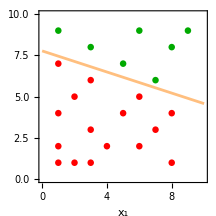

```mathematica
λ=.003;
wd=svmTrainPrimal[xndTrain,ynTrain,λ];
(*-------- MAKE THE PLOTS  --------*)
visualize[]
```

## Initialization cells

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={BaseStyle->{14,FontFamily->"Times",Black}};
myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black},ImageMargins->1};
myPS1={PlotStyle->ColorData[97]};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS,myPS1];
SetOptions[ListLinePlot,myGS,myPS,myPS1];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[DiscretePlot,myGS,myPS];
SetOptions[RectangleChart,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myRealPlot and myComplexPlot

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```